# TreePatterns 1.08

## documentation notebook

Eric Rowland
https://ericrowland.github.io/packages.html

## Introduction

TreePatterns is a package for studying trees that avoid a given tree pattern.
This introduction gets you started with a few features of the package; the next section provides a complete list of package symbols along with their usage messages and further examples.

TreePatterns uses functions from my package BinaryTrees, so you will need to have BinaryTrees installed as well.

To use TreePatterns, first you will need to load the package by evaluating the following cell.  (If you need help, see loading a package.)

```mathematica
<<TreePatterns`
```

### Representing trees

A rooted tree is represented by an expression in which each vertex corresponds to a list containing its children.  For example, here is a 5-leaf binary tree:

```mathematica
{{{},{}},{{{},{}},{}}}
```

The Wolfram Language symbol TreeForm displays expressions graphically.  BareTreeForm uses TreeForm to draw trees without vertex labels:

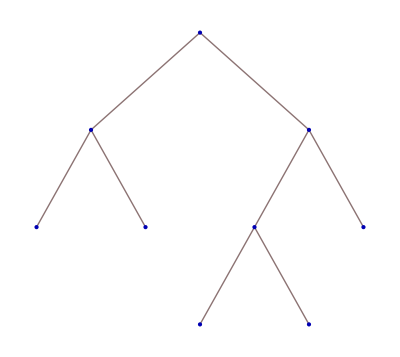

```mathematica
BareTreeForm[{{{},{}},{{{},{}},{}}}]
```

BinaryTrees gives a list of all binary trees with a fixed number of leaves.

{{{},{{},{{},{}}}},{{},{{{},{}},{}}},{{{},{}},{{},{}}},{{{},{{},{}}},{}},{{{{},{}},{}},{}}}

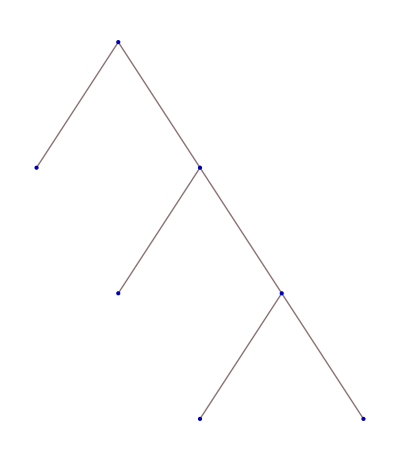
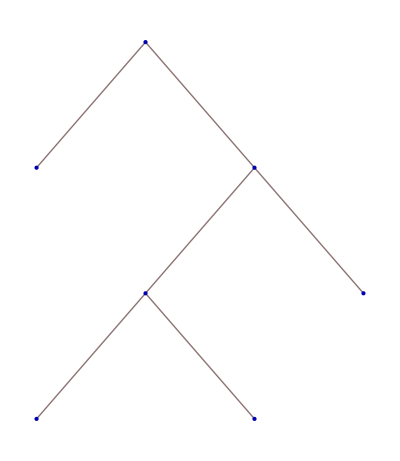
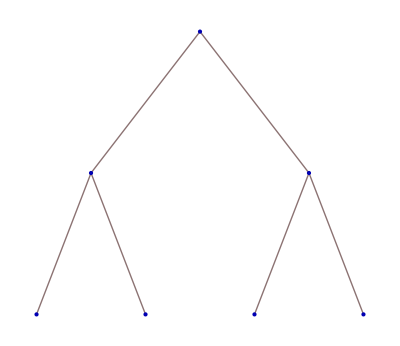
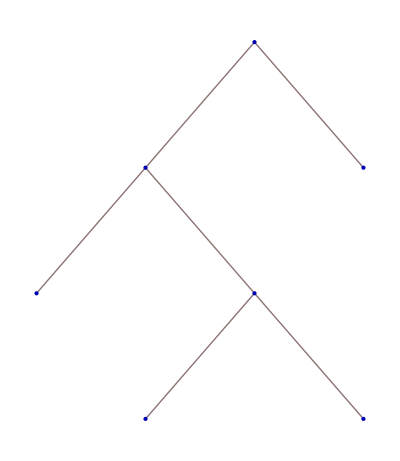
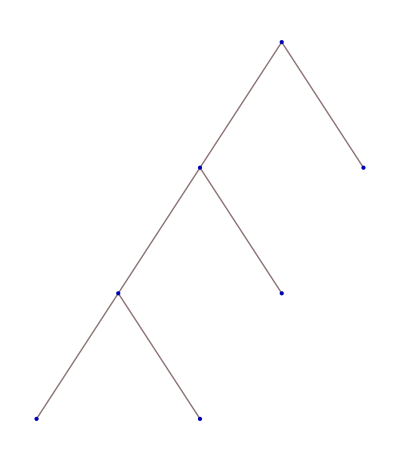

```mathematica
BinaryTrees[4]
BareTreeForm/@%
```

### Tree patterns and specific bijections

Pattern matching functionality in the Wolfram Language provides a convenient way to compute (by exhaustive search) how many binary trees do not contain another binary tree as a contiguous subtree.

First we need to render a tree as a pattern.

```mathematica
BinaryTrees[4]⟦-1⟧
```

{{{{},{}},{}},{}}

```mathematica
TreePattern[{{{{},{}},{}},{}}]
```

{{{{___},{___}},{___}},{___}}

Now we can use this pattern in, for example, FreeQ.
For the particular tree, we get the sequence of Motzkin numbers.

```mathematica
Table[Length[Select[BinaryTrees[n],Function[binarytree,FreeQ[binarytree,{{{{___},{___}},{___}},{___}}]]]],{n,10}]
```

{1,1,2,4,9,21,51,127,323,835}

BinaryTree45Bijection is an explicit bijection between binary trees avoiding {{{{___},{___}},{___}},{___}} and Motzkin paths.
(The name comes from this tree being indexed as the fifth binary tree on four leaves.)

```mathematica
BinaryTree45Bijection/@Select[BinaryTrees[5],Function[binarytree,FreeQ[binarytree,{{{{___},{___}},{___}},{___}}]]]
```

{{0,0,0,0},{0,0,1,-1},{0,1,-1,0},{0,1,0,-1},{1,-1,0,0},{1,-1,1,-1},{1,0,-1,0},{1,0,0,-1},{1,1,-1,-1}}

The inverse is BinaryTree45BijectionInverse.

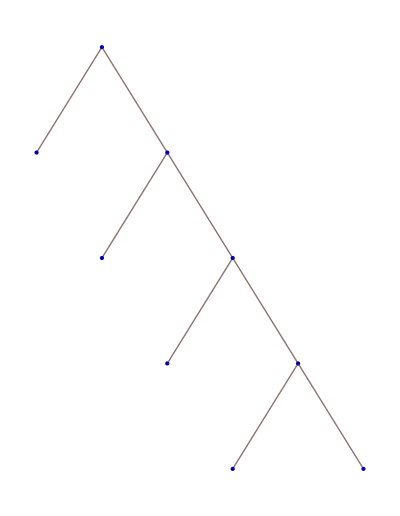
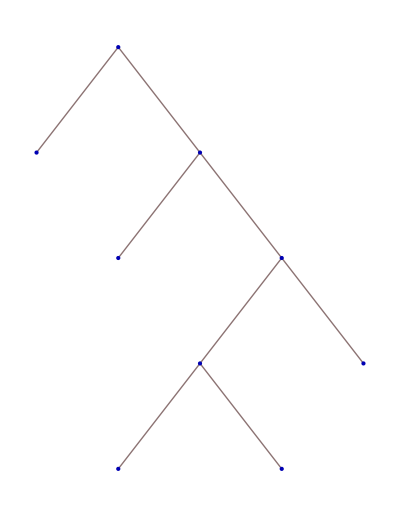
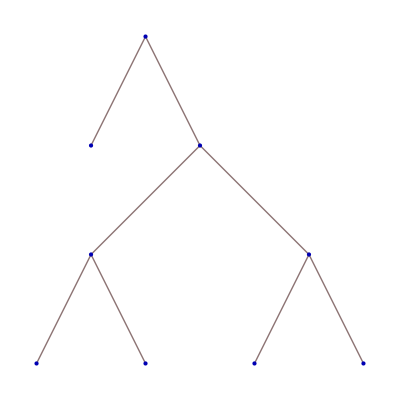
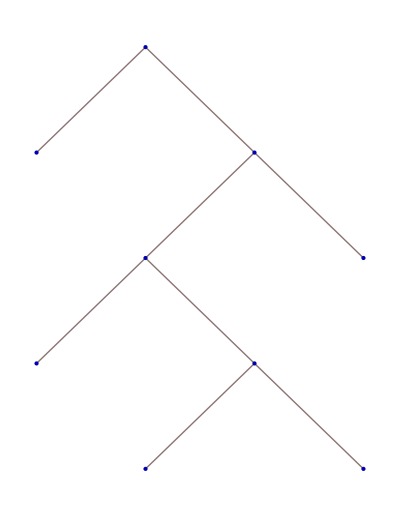
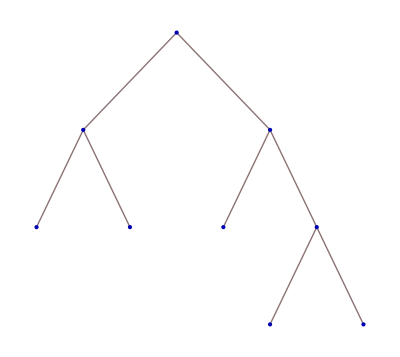
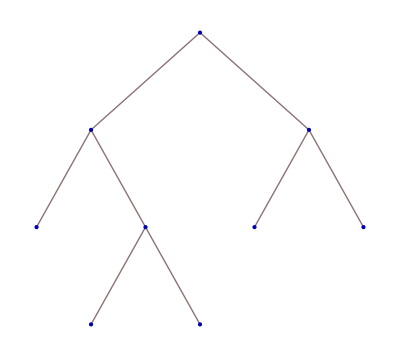
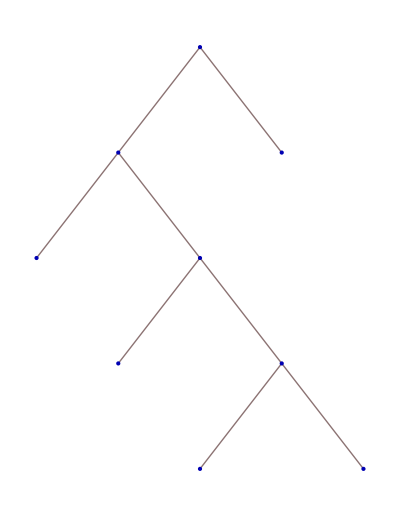
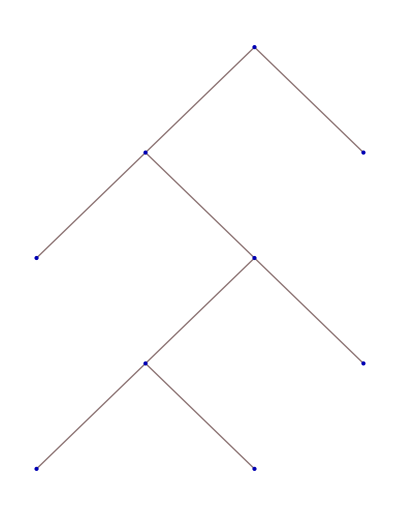
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@BinaryTree45BijectionInverse/@%
```

### Computing the number of binary trees avoiding a given pattern

One way to more efficiently determine the number of binary trees avoiding a given tree pattern t is to first compute the generating function counting n-vertex binary trees avoiding t, which is always algebraic, and then extract the desired coefficient.  AvoidingWeightEquation gives a polynomial equation that the generating function satisfies.

```mathematica
AvoidingWeightEquation[{{{{},{}},{}},{}},f,x]
```

-f+x+f x^2+f^2 x^3==0

ImplicitSeries from my IntegerSequences package gives the explicit coefficients of f.

```mathematica
Needs["IntegerSequences`"]
ImplicitSeries[x-f[x]+x^2 f[x]+x^3 f[x]^2==0,f[x],{x,0,20}]
```

{{f[x]→x+x^3+2 x^5+4 x^7+9 x^9+21 x^11+51 x^13+127 x^15+323 x^17+835 x^19+O[x]^21}}

More generally, WeightEquation computes a polynomial equation satisfied by the generating function counting all binary trees with respect to multiple tree patterns.

```mathematica
WeightEquation[{{},{{},{}}},{{{{},{}},{}},{}},f,x]
```

f-x[{}]-x[{}]^3-x[{}]^5-f x[{}]^2 x[{{},{{},{}}}]+x[{}]^3 x[{{},{{},{}}}]-2 f x[{}]^4 x[{{},{{},{}}}]+2 x[{}]^5 x[{{},{{},{}}}]-f^2 x[{}]^3 x[{{},{{},{}}}]^2+2 f x[{}]^4 x[{{},{{},{}}}]^2-x[{}]^5 x[{{},{{},{}}}]^2-f x[{}]^2 x[{{{{},{}},{}},{}}]+x[{}]^3 x[{{{{},{}},{}},{}}]+x[{}]^5 x[{{{{},{}},{}},{}}]-f^2 x[{}] x[{{},{{},{}}}] x[{{{{},{}},{}},{}}]+2 f x[{}]^2 x[{{},{{},{}}}] x[{{{{},{}},{}},{}}]-x[{}]^3 x[{{},{{},{}}}] x[{{{{},{}},{}},{}}]+2 f x[{}]^4 x[{{},{{},{}}}] x[{{{{},{}},{}},{}}]-2 x[{}]^5 x[{{},{{},{}}}] x[{{{{},{}},{}},{}}]+f^2 x[{}]^3 x[{{},{{},{}}}]^2 x[{{{{},{}},{}},{}}]-2 f x[{}]^4 x[{{},{{},{}}}]^2 x[{{{{},{}},{}},{}}]+x[{}]^5 x[{{},{{},{}}}]^2 x[{{{{},{}},{}},{}}]==0

```mathematica
%/.{x[{}]->x,x[{{},{{},{}}}]->y,x[{{{{},{}},{}},{}}]->z}
```

f-x-x^3-x^5-f x^2 y+x^3 y-2 f x^4 y+2 x^5 y-f^2 x^3 y^2+2 f x^4 y^2-x^5 y^2-f x^2 z+x^3 z+x^5 z-f^2 x y z+2 f x^2 y z-x^3 y z+2 f x^4 y z-2 x^5 y z+f^2 x^3 y^2 z-2 f x^4 y^2 z+x^5 y^2 z==0

### Equivalence of tree patterns and general bijections

Two tree patterns s and t are equivalent if for all n the number of n-leaf binary trees avoiding s is the same as the number of n-leaf binary trees avoiding t.  One can determine equivalence simply by computing the polynomial equations satisfied by the generating functions corresponding to the two tree patterns.

BinaryTreeClassData contains precomputed data about the equivalence classes of binary trees.  It works much like one of the standard Mathematica data paclets (GraphData, PolyhedronData, etc.).

```mathematica
BinaryTreeClassData["Properties"]
```

{AvoidingSequenceNumber,AvoidingWeightEquation,EquivalenceGraphImage,Indices,Members,ProbableAvoidingBijections,StatisticIdentifier,WeightEquation}

There are three equivalence classes of 5-leaf binary trees:

```mathematica
BinaryTreeClassData[5]
```

{{5,1},{5,2},{5,3}}

Here are the members of those equivalence classes:

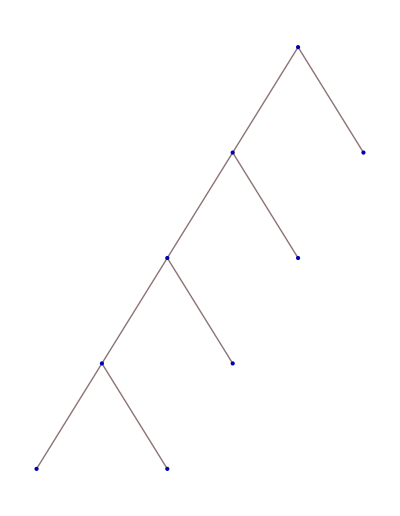
{-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@BinaryTreeClassData[{5,1},"Members"]
```

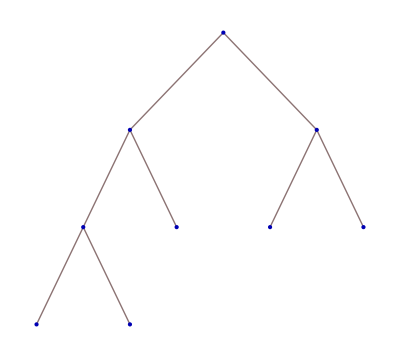
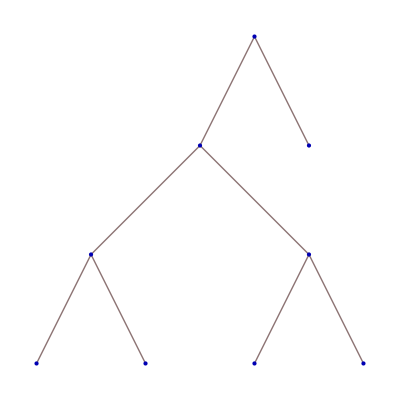
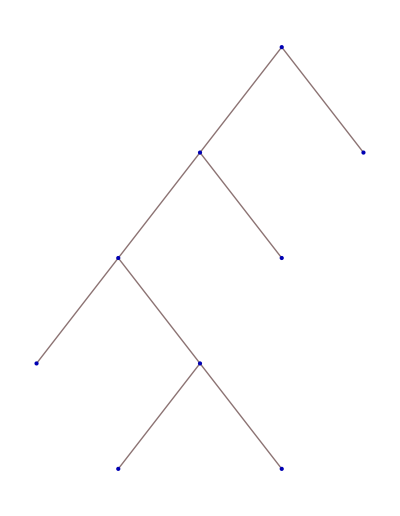
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@BinaryTreeClassData[{5,2},"Members"]
```

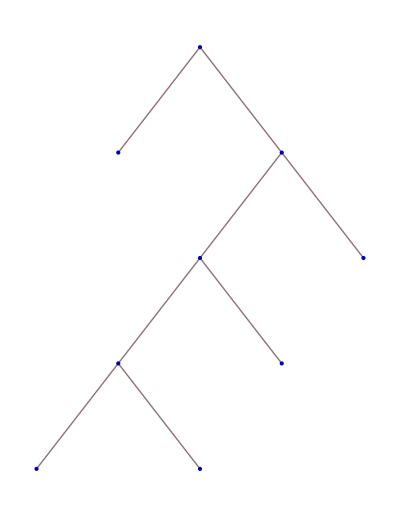
{-Graphics-,-Graphics-}

```mathematica
BareTreeForm/@BinaryTreeClassData[{5,3},"Members"]
```

```mathematica
BareTreeForm/@BinaryTrees[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Given two equivalent tree patterns, one would like an explicit bijection between the respective sets of n-leaf trees avoiding them.  Often a bijection can be accomplished by a top-down or bottom-up replacement of one leaf pattern by the other.

Such a replacement is determined by the permutation of leaves.  ProbableAvoidingBijections finds permutations that produce bijections under the assumption that several overlapped patterns never break the bijection.

```mathematica
ProbableAvoidingBijections[BinaryTrees[5]⟦2⟧,BinaryTrees[5]⟦3⟧]
```

{{1,3,4,2,5}}

TreeReplacementRules turns the permutation into explicit rules, and TopDownReplaceAll performs the top-down replacement.

```mathematica
rules=TreeReplacementRules[BinaryTrees[5]⟦2⟧,BinaryTrees[5]⟦3⟧,{1,3,4,2,5}]
```

{{$1_,{$2_,{{$3_,$4_},$5_}}}:>{$1,{{$3,$4},{$2,$5}}},{$1_,{{$3_,$4_},{$2_,$5_}}}:>{$1,{$2,{{$3,$4},$5}}}}

Applying the top-down replacement to a tree avoiding the first pattern produces a tree that avoids the second pattern:

```mathematica
And@@(FreeQ[TopDownReplaceAll[#1,rules],TreePattern[BinaryTrees[5]⟦3⟧]]&)/@Select[BinaryTrees[7],FreeQ[#1,TreePattern[BinaryTrees[5]⟦2⟧]]&]
```

True

```mathematica
Clear[rules]
```

For the nontrivial equivalence class of 5-leaf binary trees, the following graph shows which tree patterns can be proven equivalent by a top-down replacement (solid red edges) and which patterns are equivalent by left–right reflection (dashed gray edges).

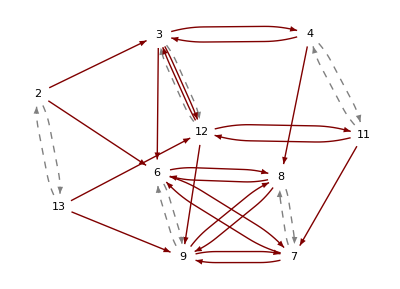

```mathematica
BinaryTreeClassData[{5,2},"EquivalenceGraphImage"]
```

## Package symbols

#### Bijections

```mathematica
?Bijections
```

RowBox[List["Bijections", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]]]], "]"]] gives the leaf permutations of SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] that produce top-down (and also bottom-up) replacement bijections in which SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]] are exchanged.

For each pair of 4-leaf binary trees, compute the permutations that induce top-down replacement bijections:

```mathematica
Grid[Outer[If[#1≠#2,Column[Bijections[##1]]]&,BinaryTrees[4],BinaryTrees[4],1]]
```

| {1,3,4,2} | {3,4,2,1} | {2,3,4,1} | 
{1,4,2,3} |  | {2,3,1,4} |  | {2,3,4,1}
{4,3,1,2} | {3,1,2,4} |  | {1,3,4,2} | {3,4,2,1}
{4,1,2,3} |  | {1,4,2,3} |  | {2,3,1,4}
 | {4,1,2,3} | {4,3,1,2} | {3,1,2,4} |

#### BinaryTree42Bijection and BinaryTree42BijectionInverse

```mathematica
?BinaryTree42Bijection
```

RowBox[List["BinaryTree42Bijection", "[", StyleBox["tree", "TI"], "]"]] gives the binary tuple corresponding to a binary tree avoiding {{___}, {{{___}, {___}}, {___}}}.

```mathematica
BinaryTree42Bijection/@Select[BinaryTrees[5],Function[binarytree,FreeQ[binarytree,TreePattern[BinaryTrees[4]⟦2⟧]]]]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

```mathematica
?BinaryTree42BijectionInverse
```

RowBox[List["BinaryTree42BijectionInverse", "[", StyleBox["list", "TI"], "]"]] gives the binary tree avoiding {{___}, {{{___}, {___}}, {___}}} corresponding to a binary tuple.

```mathematica
BareTreeForm/@BinaryTree42BijectionInverse/@%%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### BinaryTree43Bijection and BinaryTree43BijectionInverse

```mathematica
?BinaryTree43Bijection
```

RowBox[List["BinaryTree43Bijection", "[", StyleBox["tree", "TI"], "]"]] gives the binary tuple corresponding to a binary tree avoiding {{{___}, {___}}, {{___}, {___}}}.

```mathematica
BinaryTree43Bijection/@Select[BinaryTrees[5],Function[binarytree,FreeQ[binarytree,TreePattern[BinaryTrees[4]⟦3⟧]]]]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

```mathematica
?BinaryTree43BijectionInverse
```

RowBox[List["BinaryTree43BijectionInverse", "[", StyleBox["list", "TI"], "]"]] gives the binary tree avoiding {{{___}, {___}}, {{___}, {___}}} corresponding to a binary tuple.

```mathematica
BareTreeForm/@BinaryTree43BijectionInverse/@%%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### BinaryTree45Bijection and BinaryTree45BijectionInverse

```mathematica
?BinaryTree45Bijection
```

RowBox[List["BinaryTree45Bijection", "[", StyleBox["tree", "TI"], "]"]] gives the Motzkin path corresponding to a binary tree avoiding {{{{___}, {___}}, {___}}, {___}}.

```mathematica
BinaryTree45Bijection/@Select[BinaryTrees[5],Function[binarytree,FreeQ[binarytree,TreePattern[BinaryTrees[4]⟦5⟧]]]]
```

{{0,0,0,0},{0,0,1,-1},{0,1,-1,0},{0,1,0,-1},{1,-1,0,0},{1,-1,1,-1},{1,0,-1,0},{1,0,0,-1},{1,1,-1,-1}}

```mathematica
?BinaryTree45BijectionInverse
```

RowBox[List["BinaryTree45BijectionInverse", "[", StyleBox["motzkinpath", "TI"], "]"]] gives the binary tree avoiding {{{{___}, {___}}, {___}}, {___}} corresponding to a Motzkin path on RowBox[List["{", RowBox[List[RowBox[List["-", StyleBox["1", "TR"]]], ",", StyleBox["0", "TR"], ",", StyleBox["1", "TR"]]], "}"]].

```mathematica
BareTreeForm/@BinaryTree45BijectionInverse/@%%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### BinaryTreeClassData

```mathematica
?BinaryTreeClassData
```

RowBox[List["BinaryTreeClassData", "[", RowBox[List[StyleBox["class", "TI"], ",", StyleBox["\"\!\(\*StyleBox[\"property\",\"TI\"]\)\"", ShowStringCharacters->True]]], "]"]] gives the value of the specified property for an equivalence class of binary trees.
RowBox[List["BinaryTreeClassData", "[", StyleBox["n", "TI"], "]"]] gives the equivalence classes of StyleBox["n", "TI"]-leaf binary trees.

Display the equivalence classes of 6-leaf binary trees:

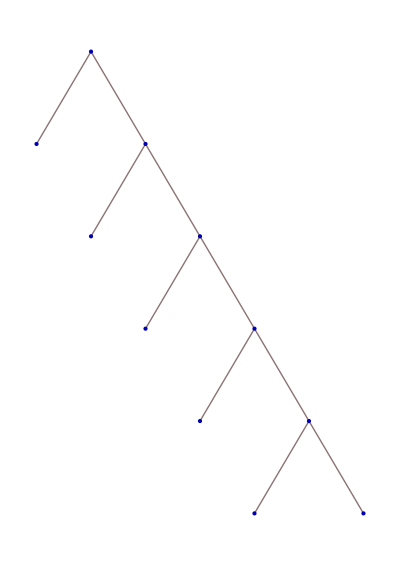
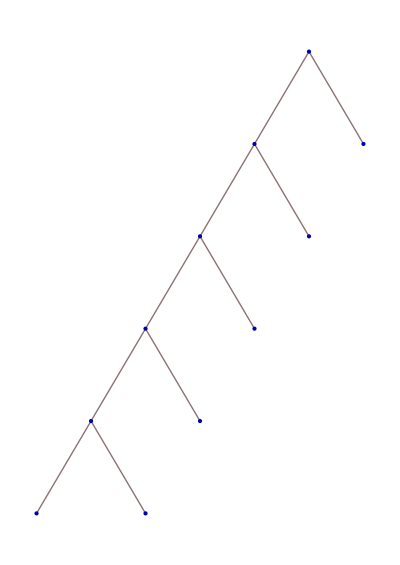
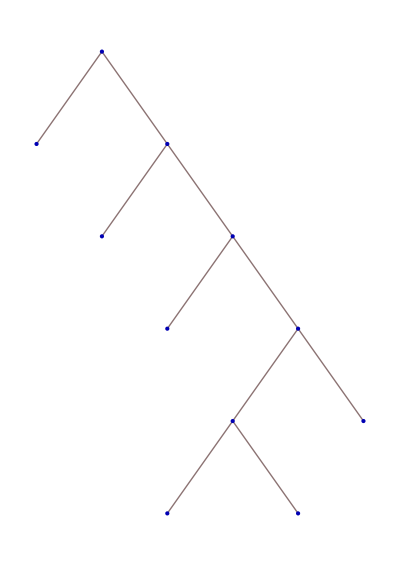
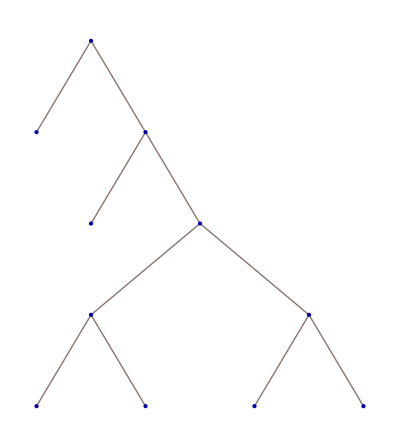
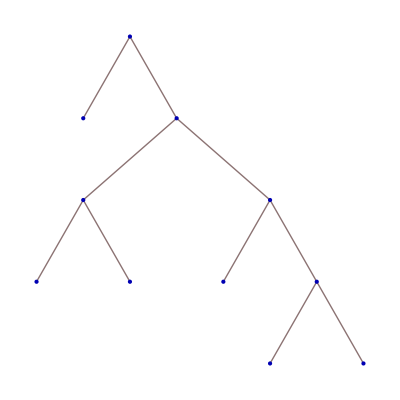
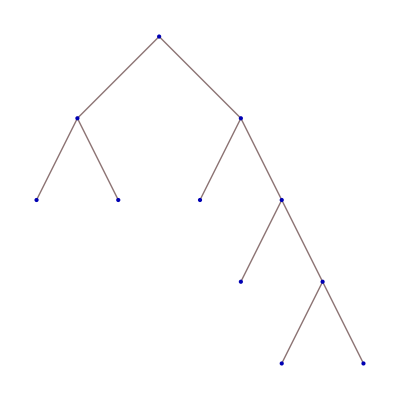
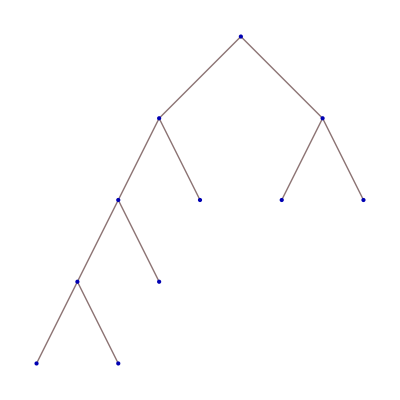
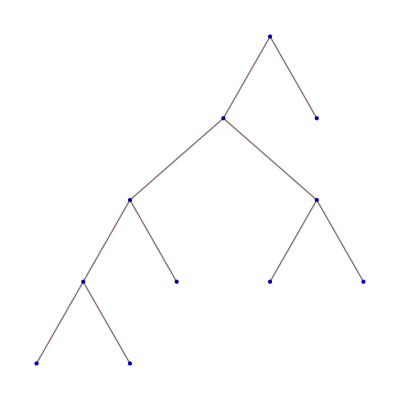

```mathematica
(BareTreeForm/@BinaryTreeClassData[#1,"Members"]&)/@BinaryTreeClassData[6]
```

Compute the polynomial equation satisfied by the generating function for binary trees with respect to number of vertices and number of instances of a given tree from class 6.3:

```mathematica
BinaryTreeClassData[{6,3},"WeightEquation"][f,x,y]
```

x-x^3+x^3 y+f (-1+2 x^2-2 x^4-2 x^2 y+2 x^4 y)+f^2 (2 x^3-x^5+x y-2 x^3 y+x^5 y)==0

Compute the number of equivalence classes of n-leaf binary trees for 1≤n≤8:

```mathematica
Length/@BinaryTreeClassData/@Range[8]
```

{1,1,1,2,3,7,15,44}

#### BinaryTreePatternQ

```mathematica
?BinaryTreePatternQ
```

RowBox[List["BinaryTreePatternQ", "[", StyleBox["expr", "TI"], "]"]] yields True if StyleBox["expr", "TI"] is a binary tree pattern, and False otherwise.

```mathematica
BinaryTreePatternQ[{{___},{___}}]
```

True

```mathematica
BinaryTreePatternQ[{{___},{___},{___}}]
```

False

#### BottomUpReplaceAll and TopDownReplaceAll

```mathematica
?BottomUpReplaceAll
```

RowBox[List["BottomUpReplaceAll", "[", RowBox[List[StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"]]], "]"]] applies a rule or list of rules in an attempt to transform each subpart of StyleBox["expr", "TI"] up from the bottom.

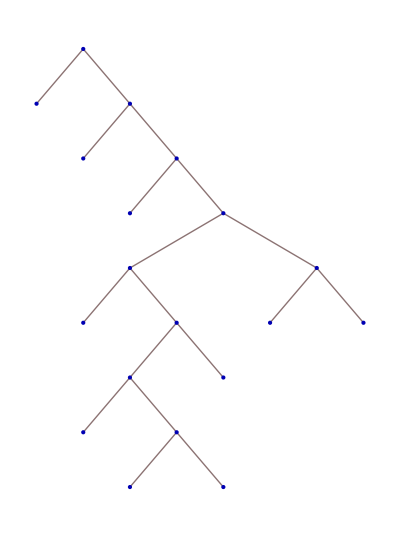

```mathematica
rule={$1_,{$2_,{{$3_,$4_},$5_}}}:>{$1,{{$3,$4},{$2,$5}}};
tree={{},{{},{{},{{{},{{{},{{},{}}},{}}},{{},{}}}}}};
BareTreeForm[tree]
```

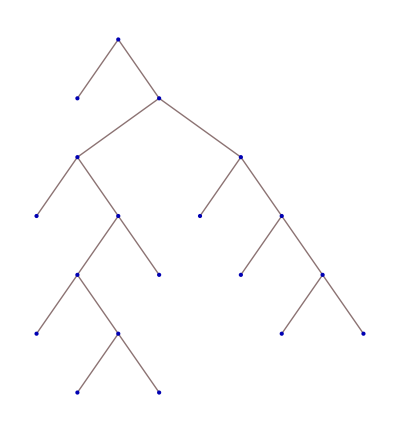

```mathematica
BareTreeForm[BottomUpReplaceAll[tree,rule]]
```

```mathematica
?TopDownReplaceAll
```

RowBox[List["TopDownReplaceAll", "[", RowBox[List[StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"]]], "]"]] applies a rule or list of rules in an attempt to transform each subpart of StyleBox["expr", "TI"] down from the top.

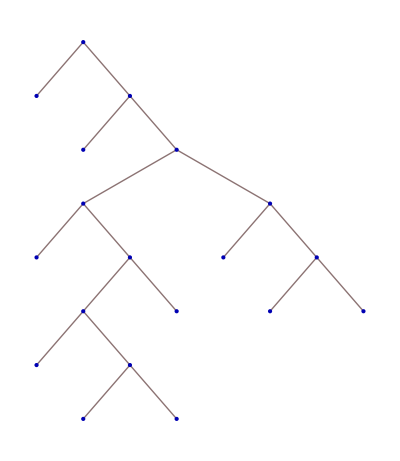

```mathematica
BareTreeForm[TopDownReplaceAll[tree,rule]]
```

```mathematica
Clear[rule,tree]
```

#### FindOverlaps

```mathematica
?FindOverlaps
```

RowBox[List["FindOverlaps", "[", RowBox[List[SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]]]], "]"]] gives the positions of all sub(tree patterns) in SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]] that have a non-full intersection with tree pattern SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]].
In other words, it finds the places in SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]] where SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]] can be hung.

```mathematica
tree1=BinaryTrees[4]⟦2⟧;
tree2=BinaryTrees[4]⟦3⟧;
BareTreeForm/@{tree1,tree2}
```

{-Graphics-,-Graphics-}

```mathematica
FindOverlaps[TreePattern[tree1],TreePattern[tree2]]
```

{{2,1},{2},{}}

```mathematica
?Leaves
```

Leaves is an option for FindOverlaps that specifies whether to allow matches at the leaves.

```mathematica
FindOverlaps[TreePattern[tree1],TreePattern[tree2],Leaves->True]
```

{{1},{2,1,1},{2,1,2},{2,1},{2,2},{2},{}}

```mathematica
Clear[tree1,tree2]
```

#### MatchingTrees and NonMatchingTrees

```mathematica
?MatchingTrees
```

RowBox[List["MatchingTrees", "[", StyleBox["treepattern", "TI"], "]"]] gives a list of tree patterns such that every tree matching StyleBox["treepattern", "TI"] matches precisely one tree pattern in the list.

```mathematica
MatchingTrees[TreePattern[BinaryTrees[4]⟦1⟧]]
```

{{{},{{},{{},{}}}},{{},{{},{{},{{___},{___}}}}},{{},{{},{{{___},{___}},{}}}},{{},{{},{{{___},{___}},{{___},{___}}}}},{{},{{{___},{___}},{{},{}}}},{{},{{{___},{___}},{{},{{___},{___}}}}},{{},{{{___},{___}},{{{___},{___}},{}}}},{{},{{{___},{___}},{{{___},{___}},{{___},{___}}}}},{{{___},{___}},{{},{{},{}}}},{{{___},{___}},{{},{{},{{___},{___}}}}},{{{___},{___}},{{},{{{___},{___}},{}}}},{{{___},{___}},{{},{{{___},{___}},{{___},{___}}}}},{{{___},{___}},{{{___},{___}},{{},{}}}},{{{___},{___}},{{{___},{___}},{{},{{___},{___}}}}},{{{___},{___}},{{{___},{___}},{{{___},{___}},{}}}},{{{___},{___}},{{{___},{___}},{{{___},{___}},{{___},{___}}}}}}

```mathematica
?NonMatchingTrees
```

RowBox[List["NonMatchingTrees", "[", StyleBox["treepattern", "TI"], "]"]] gives a list of tree patterns such that every tree not matching StyleBox["treepattern", "TI"] matches precisely one tree pattern in the list.

{{},{{___},{}},{{___},{{___},{}}}}

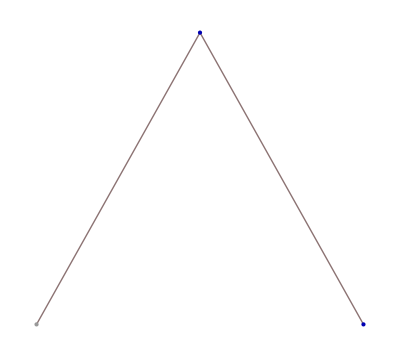
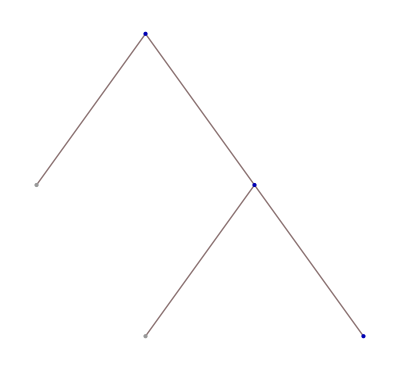
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
NonMatchingTrees[TreePattern[BinaryTrees[4]⟦1⟧]]
BareTreeForm/@%
```

#### PatternIntersection

```mathematica
?PatternIntersection
```

RowBox[List["PatternIntersection", "[", RowBox[List[SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"]]], "]"]] gives a pattern which is matched by any expression matching all of the tree patterns RowBox[List[SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"]]].

```mathematica
tree1=BinaryTrees[4]⟦2⟧;
tree2=BinaryTrees[4]⟦3⟧;
BareTreeForm/@{tree1,tree2}
```

{-Graphics-,-Graphics-}

{{{___},{___}},{{{___},{___}},{___}}}

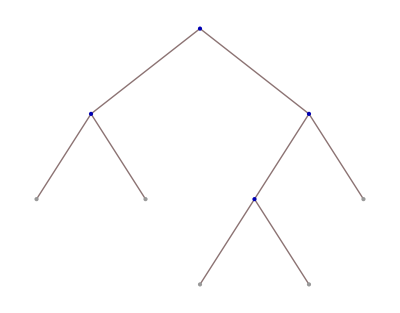

```mathematica
PatternIntersection[TreePattern[tree1],TreePattern[tree2]]
BareTreeForm[%]
```

```mathematica
Clear[tree1,tree2]
```

#### ProbableAvoidingBijectionQ

```mathematica
?ProbableAvoidingBijectionQ
```

RowBox[List["ProbableAvoidingBijectionQ", "[", RowBox[List[SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["rules", "TI"]]], "]"]] determines whether the bijection given by StyleBox["rules", "TI"] induces a top-down replacement bijection from trees avoiding SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]] to trees avoiding SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], assuming that the patterns are sufficiently shallow that three overlapping patterns in a tree does not cause problems.

```mathematica
ProbableAvoidingBijectionQ[TreePattern[BinaryTrees[4]⟦2⟧],TreePattern[BinaryTrees[4]⟦3⟧],{{$2_,$3_},{$1_,$4_}}:>{$1,{{$2,$3},$4}}]
```

True

```mathematica
ProbableAvoidingBijectionQ[TreePattern[BinaryTrees[4]⟦2⟧],TreePattern[BinaryTrees[4]⟦3⟧],{$1_,{{$2_,$3_},$4_}}:>{{$2,$3},{$1,$4}}]
```

False

#### ProbableAvoidingBijections

```mathematica
?ProbableAvoidingBijections
```

RowBox[List["ProbableAvoidingBijections", "[", RowBox[List[SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]]]], "]"]] gives a list of the permutations that provide top-down replacement bijections on the set of binary trees and induce bijections from trees avoiding SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]] to trees avoiding SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]], assuming that the patterns are sufficiently shallow that three overlapping patterns in a tree does not cause problems.

```mathematica
ProbableAvoidingBijections[BinaryTrees[4]⟦2⟧,BinaryTrees[4]⟦3⟧]
```

{{2,3,1,4}}

#### TreePattern and FromTreePattern

```mathematica
?TreePattern
```

RowBox[List["TreePattern", "[", StyleBox["tree", "TI"], "]"]] forms a tree pattern by replacing each leaf {} of StyleBox["tree", "TI"] by {___}.

```mathematica
TreePattern[BinaryTrees[5]⟦5⟧]
```

{{___},{{{{___},{___}},{___}},{___}}}

```mathematica
?FromTreePattern
```

RowBox[List["FromTreePattern", "[", StyleBox["treepattern", "TI"], "]"]] forms a tree by replacing each leaf {__} or {___} of StyleBox["treepattern", "TI"] by {}.

```mathematica
FromTreePattern[{{___},{{{{___},{___}},{___}},{___}}}]
```

{{},{{{{},{}},{}},{}}}

#### TreeReplacementRules

```mathematica
?TreeReplacementRules
```

RowBox[List["TreeReplacementRules", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]], ",", StyleBox["perm", "TI"]]], "]"]] gives a list containing the rule for replacing SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] with SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]] according to the given permutation of leaves, and its inverse.

```mathematica
TreeReplacementRules[BinaryTrees[4]⟦1⟧,BinaryTrees[4]⟦2⟧,{1,3,2,4}]
```

{{$1_,{$2_,{$3_,$4_}}}:>{$1,{{$3,$2},$4}},{$1_,{{$3_,$2_},$4_}}:>{$1,{$2,{$3,$4}}}}

#### Weight

```mathematica
?Weight
```

RowBox[List["Weight", "[", RowBox[List[StyleBox["tree", "TI"], ",", StyleBox["t", "TI"], ",", StyleBox["x", "TI"]]], "]"]] computes the weight of a binary tree with respect to the tree StyleBox["t", "TI"].
RowBox[List["Weight", "[", RowBox[List[StyleBox["tree", "TI"], ",", RowBox[List["{", RowBox[List[SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["k", "TI"]]]], "}"]], ",", RowBox[List["{", RowBox[List[SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["k", "TI"]]]], "}"]]]], "]"]] computes the weight of a binary tree with respect to several trees.

```mathematica
BareTreeForm[BinaryTrees[5]⟦10⟧]
Weight[BinaryTrees[5]⟦10⟧,{{},{}},x]
```

-Graphics-

x^4

```mathematica
Weight[BinaryTrees[5]⟦10⟧,{{},{{},{}},{{},{{},{}}}},{x,y,z}]
```

x^9 y^4 z^2

#### WeightEquation and AvoidingWeightEquation

```mathematica
?AvoidingWeightEquation
```

RowBox[List["AvoidingWeightEquation", "[", RowBox[List[StyleBox["t", "TI"], ",", StyleBox["f", "TI"], ",", StyleBox["x", "TI"]]], "]"]] gives an equation satisfied by the weight StyleBox["f", "TI"] of the set of binary trees that avoid the tree StyleBox["t", "TI"], where the weight of a tree is SuperscriptBox[StyleBox["x", "TI"], StyleBox["number of vertices", "TI"]].

The five binary trees with 4 leaves and polynomial equations satisfied by the generating function counting binary trees that avoid each:

```mathematica
Grid[({BareTreeForm[#1],AvoidingWeightEquation[#1,f,x]}&)/@BinaryTrees[4]]
```

-Graphics- | -f+x+f x^2+f^2 x^3==0
-Graphics- | f-x-2 f x^2+x^3==0
-Graphics- | f-x-2 f x^2+x^3==0
-Graphics- | f-x-2 f x^2+x^3==0
-Graphics- | -f+x+f x^2+f^2 x^3==0

```mathematica
?WeightEquation
```

RowBox[List["WeightEquation", "[", RowBox[List[StyleBox["t", "TI"], ",", StyleBox["f", "TI"], ",", StyleBox["x", "TI"]]], "]"]] gives an equation satisfied by the weight StyleBox["f", "TI"] of the set of binary trees, where the weight of a tree is RowBox[List[SuperscriptBox[RowBox[List[StyleBox["x", "TI"], "[", RowBox[List["{", "}"]], "]"]], StyleBox["number of vertices", "TI"]], " ", SuperscriptBox[RowBox[List[StyleBox["x", "TI"], "[", StyleBox["t", "TI"], "]"]], StyleBox["number of occurrences of t", "TI"]]]].
RowBox[List["WeightEquation", "[", RowBox[List[SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["k", "TI"]], ",", StyleBox["f", "TI"], ",", StyleBox["x", "TI"]]], "]"]] uses the weight function RowBox[List[SuperscriptBox[RowBox[List[StyleBox["x", "TI"], "[", RowBox[List["{", "}"]], "]"]], StyleBox["number of vertices", "TI"]], " ", RowBox[List[UnderoverscriptBox["\[Product]", RowBox[List[StyleBox["i", "TI"], "=", StyleBox["1", "TR"]]], StyleBox["k", "TI"]], SuperscriptBox[RowBox[List[StyleBox["x", "TI"], "[", SubscriptBox[StyleBox["t", "TI"], StyleBox["i", "TI"]], "]"]], RowBox[List[StyleBox["number of occurrences of", "TI"], " ", SubscriptBox[StyleBox["t", "TI"], StyleBox["i", "TI"]]]]]]]]].

More generally, we can count all binary trees with respect to number of vertices and number of occurrences of a given 4-leaf pattern:
Setting y=0 gives the equations satisfied by the avoiding generating function.

```mathematica
Grid[({BareTreeForm[#1],WeightEquation[#1,f,x]/.{x[{}]->x,x[#1]->y}}&)/@BinaryTrees[4]]
```

-Graphics- | f-x-f x^2-f^2 x^3-f^2 x y+f x^2 y+f^2 x^3 y==0
-Graphics- | -f+x+2 f x^2-x^3+f^2 x y-2 f x^2 y+x^3 y==0
-Graphics- | -f+x+2 f x^2-x^3+f^2 x y-2 f x^2 y+x^3 y==0
-Graphics- | -f+x+2 f x^2-x^3+f^2 x y-2 f x^2 y+x^3 y==0
-Graphics- | f-x-f x^2-f^2 x^3-f^2 x y+f x^2 y+f^2 x^3 y==0